```mathematica
ClearAll["Global`*"];
```

```mathematica
α=45;             (* deg *)
```

```mathematica
g=9.81;         (* m/s^2 *)
```

```mathematica
vx=vo×cos(α °);
```

```mathematica
m1=(1-x)×m;
m2=x×m;
```

```mathematica
pp=m×vx;
p1=-m1×v1;
p2=m2×v2;
```

```mathematica
A=Solve[{ p1+p2==pp,v1==vx},v2,v1];
```

Solve::bdomv: Warning: v1 is not a valid domain specification. Mathematica is assuming it is a variable to eliminate.

```mathematica
zuk=(vo^2×sin(2×α °))/g;
huk=(vo^2×sin^2(α °))/(2×g);
zpoz=v2×√((2×huk)/g)/.A;
```

```mathematica
s=1/2×zuk+zpoz;
```

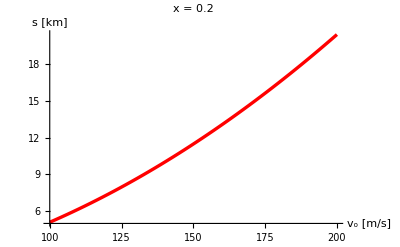

```mathematica
rys1=Plot[s×10^-3/.x->0.2,{vo,100,200},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     x = 0.2  ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v_o [m/s]","s [km] "}]
```

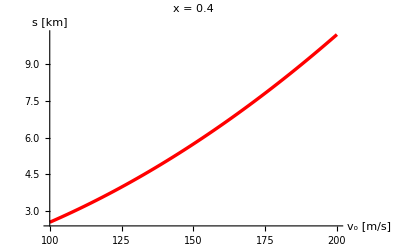

```mathematica
rys2=Plot[s×10^-3/.x->0.4,{vo,100,200},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     x = 0.4  ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v_o [m/s]","s [km] "}]
```